```mathematica
ClearAll[m0];ClearAll[Γ0];ClearAll[S];ClearAll[L0];ClearAll[J0];ClearAll[decays];
configuration="PDG";
 FILL IN ALL DECAY CHANNEL ANGULAR MOMENTA FOR ALL DECAYS!!!
(** Nucleons **)
m0[N938]=0.938;Γ0[N938]=0.;S[N938]=1/2;L0[N938]=0;J0[N938]=1/2;

m0[N1535]=1.530;Γ0[N1535]=0.150;S[N1535]=1/2;J0[N1535]=1/2;
decays[N1535]={
{{N938,pi},0.42},
{{N938,eta},0.45},
{{N938,sigma},0.06},
{{N1440,pi},0.07}
};

m0[N1650]=1.650;Γ0[N1650]=0.125;S[N1650]=1/2;J0[N1650]=1/2;
decays[N1650]={
{{N938,pi},0.56},
{{N938,eta},0.15},
{{Lambda,Ka},0.05},
{{Δ1232,pi},0.08},
{{N938,sigma},0.06},
{{N1440,pi},0.10}
};

m0[N1520]=1.515;Γ0[N1520]=0.115;S[N1520]=3/2;J0[N1520]=3/2;
decays[N1520]={
{{N938,pi},0.60,1},
{{D1232,pi},0.10,0},
{{D1232,pi},0.10,2},
{{N938,rho},0.20,0}
};

m0[N1700]=1.720;Γ0[N1700]=0.200;S[N1700]=3/2;L0[N1700]=1;J0[N1700]=3/2;
decays[N1700]={
{{N938,pi},0.13},
{{N938,omega},0.22},
{{Δ1232,pi},0.60},
{{N1440,pi},0.05}
};

m0[N1675]=1.675;Γ0[N1675]=0.150;S[N1675]=5/2;L0[N1675]=1;J0[N1675]=5/2;
decays[N1675]={
{{N938,pi},0.45},
{{N938,pipi},0.15},
{{Δ1232,pi},0.35},
{{N938,sigma},0.05}
};

m0[N1440]=1.430;Γ0[N1440]=0.350;S[N1440]=1/2;L0[N1440]=0;J0[N1440]=1/2;
decays[N1440]={
{{N938,pi},0.65,1},
{{Δ1232,pi},0.20,1},
{{N938,sigma},0.15,1}
};

m0[N1710]=1.710;Γ0[N1710]=0.100;S[N1710]=1/2;L0[N1710]=0;J0[N1710]=1/2;
decays[N1710]={
{{N938,pi},0.15},
{{N938,eta},0.45},
{{N938,omega},0.05},
{{Lambda,Ka},0.20},
{{N1535,pi},0.15}
};

m0[N1720]=1.720;Γ0[N1720]=0.250;S[N1720]=3/2;L0[N1720]=2;J0[N1720]=3/2;
decays[N1720]={
{{N938,pi},0.10},
{{N938,eta},0.025},
{{N938,omega},0.20},
{{Lambda,Ka},0.05},
{{Δ1232,pi},0.50},
{{N938,sigma},0.10},
{{N1440,pi},0.025}
};

m0[N1680]=1.685;Γ0[N1680]=0.120;S[N1680]=5/2;L0[N1680]=2;J0[N1680]=5/2;
decays[N1680]={
{{N938,pi},0.65},
{{Δ1232,pi},0.20},
{{N938,sigma},0.15}
};

ps={N1535, N1650, N1520, N1700, N1675, N1440, N1710, N1720, N1680 };


(** Delta particles **)
m0[Δ1232]=1.232;Γ0[Δ1232]=0.115;S[Δ1232]=3/2;L0[Δ1232]=0;J0[Δ1232]=3/2;
decays[Δ1232]={
{{N938,gamma}, 0.01},
{{N938,pi},0.99}
};

m0[Δ1620]=1.630;Γ0[Δ1620]=0.140;S[Δ1620]=1/2;L0[Δ1620]=0;J0[Δ1620]=1/2;
decays[Δ1620]={
{{N938,pi},0.25},
{{Δ1232,pi},0.70},
{{N1440,pi},0.05}
};

m0[Δ1700]=1.700;Γ0[Δ1700]=0.300;S[Δ1700]=3/2;L0[Δ1700]=0;J0[Δ1700]=3/2;
decays[Δ1700]={
{{N938,pi},0.15},
{{Δ1232,pi},0.40},
{{N938,rho},0.40},
{{Δ1232,eta},0.05}
};

m0[Δ1910]=1.900;Γ0[Δ1910]=0.300;S[Δ1910]=1/2;L0[Δ1910]=2;J0[Δ1910]=1/2;
decays[Δ1910]={
{{N938,pi},0.25},
{{Sigma,Ka},0.10},
{{Δ1232,pi},0.50},
{{N1440,pi},0.05},
{{Δ1232,eta},0.10}
};

m0[Δ1600]=1.600;Γ0[Δ1600]=0.320;S[Δ1600]=3/2;L0[Δ1600]=0;J0[Δ1600]=3/2;
decays[Δ1600]={
{{N938,pi},0.20},
{{Δ1232,pi},0.80}
};

m0[Δ1920]=1.920;Γ0[Δ1920]=0.260;S[Δ1920]=3/2;L0[Δ1920]=2;J0[Δ1920]=3/2;
decays[Δ1920]={
{{N938,pi},0.15},
{{Sigma,Ka},0.05},
{{Δ1232,pi},0.65},
{{Δ1232,eta},0.15}
};

m0[Δ1905]=1.880;Γ0[Δ1905]=0.330;S[Δ1905]=3/2;L0[Δ1905]=2;J0[Δ1905]=5/2;
decays[Δ1905]={
{{N938,pi},0.10},
{{Δ1232,pi},0.80},
{{N1680,pi},0.05},
{{Δ1232,eta},0.05}
};

m0[Δ1950]=1.930;Γ0[Δ1950]=0.285;S[Δ1950]=3/2;L0[Δ1950]=2;J0[Δ1950]=7/2;
decays[Δ1950]={
{{N938,pi},0.80},
{{Δ1232,pi},0.10},
{{N1680,pi},0.10}
};

Δs={ Δ1620, Δ1700, Δ1910, Δ1600, Δ1920, Δ1905, Δ1950 };



(** Mesons **)
m0[pi]=0.137;Γ0[pi]=0.;S[pi]=0;L0[pi]=0;J0[pi]=0;
m0[pipi]=0.274;Γ0[pipi]=0.;S[pipi]=0;L0[pipi]=0;

m0[gamma]=0.;Γ0[gamma]=0.;J0[gamma]=1;
m0[eta]=0.548;Γ0[eta]=0.;J0[eta]=0;
m0[rho]=0.775;Γ0[rho]=0.149;J0[rho]=1;
decays[rho]={ {{pi,pi},1.} };
m0[sigma]=0.500;Γ0[sigma]=0.550; J0[sigma]=1;(* AKA Subscript[f, 0](500) *)
decays[sigma]={
{{pi, pi}, 1.}
};
m0[omega]=782.65;Γ0[omega]=8.49;J0[omega]=1;
decays[omega]={
{{pi,pipi},0.9},
{{pi,pi},0.015},
{{pi,gamma},0.085}
};
m0[Lambda]=1.116;Γ0[Lambda]=0.;J0[Lambda]=1/2;
m0[Ka]=0.498;Γ0[Ka]=0.;J0[Ka]=0;
m0[Sigma]=1.190;Γ0[Sigma]=0.;J0[Sigma]=1/2;

decays[p_]:=Throw["No decays found for "<>ToString[p]];
m0[p_]:=Throw["No nominal mass found for "<>ToString[p]];
Γ0[p_]:=Throw["No nominal width found for "<>ToString[p]];
S[p_]:=Throw["No spin found for "<>ToString[p]];
L0[p_]:=Throw["No orbital angular momentum found for "<>ToString[p]];
```

```mathematica
Block[{h=N1535},
Plot[Evaluate@Flatten@{
Γ[h,m],
Table[Γ[h,outs,m],{outs,decayProducts[h]}]
},{m,1.,2.},PlotLegends->Flatten@{"Total",ToString/@decayProducts[h]}]
]
```

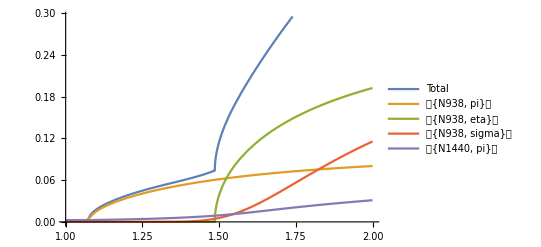

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {1.48571}. NIntegrate obtained 6.5272 and 0.0000241659 for the integral and error estimates.

Calculating aN for N1535

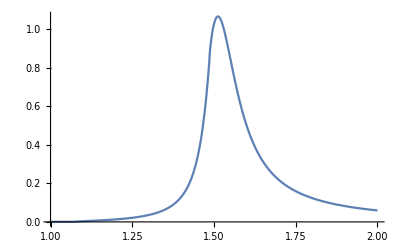

```mathematica
Block[{scale=a[N1535,m0[N1535]]/1.},
Plot[a[N1535,m]/scale,{m,1.,2.}]
]
```

```mathematica
a[N1535,m0[N1535]]/a[N1535,2.0]
```

16.8382